# OOP CISS Rotation of the initial density matrix

## Utilities

### Spin operators (product basis)

```mathematica
sx = {{0, 1}, {1, 0}}/2;
sy = {{0, -I}, {I, 0}}/2;
sz = {{1, 0}, {0, -1}}/2;
ee2x2 = {{1, 0}, {0, 1}};
zz2x2 = {{0, 0}, {0, 0}};
ee=1/2*TensorProduct[ee2x2, ee2x2]//ArrayFlatten;
sxa=TensorProduct[sx, ee2x2]//ArrayFlatten;
sya=TensorProduct[sy, ee2x2]//ArrayFlatten;
sza=TensorProduct[sz, ee2x2]//ArrayFlatten;
sxb=TensorProduct[ee2x2, sx]//ArrayFlatten;
syb=TensorProduct[ee2x2, sy]//ArrayFlatten;
szb=TensorProduct[ee2x2, sz]//ArrayFlatten;
sxx=2*TensorProduct[sx, sx]//ArrayFlatten;
sxy=2*TensorProduct[sx, sy]//ArrayFlatten;
sxz=2*TensorProduct[sx, sz]//ArrayFlatten;
syx=2*TensorProduct[sy, sx]//ArrayFlatten;
syy=2*TensorProduct[sy, sy]//ArrayFlatten;
syz=2*TensorProduct[sy, sz]//ArrayFlatten;
szx=2*TensorProduct[sz, sx]//ArrayFlatten;
szy=2*TensorProduct[sz, sy]//ArrayFlatten;
szz=2*TensorProduct[sz, sz]//ArrayFlatten;
zz = TensorProduct[zz2x2, zz2x2]//ArrayFlatten;
productBasis = {ee, sxa, sya, sza, sxb, syb, szb, sxx,sxy,sxz,syx,syy,syz, szx, szy, szz};
productBasisAlpha = {"II/2", "Sxa","Sya","Sza","Sxb","Syb","Szb","Sxx","Sxy","Sxz","Syx","Syy","Syz","Szx","Szy","Szz"};
```

### Functions

```mathematica
commutator[a_, b_] := a.b - b.a
propagator[a_, b_, ξ_] := TrigReduce[ExpToTrig[MatrixExp[-I*ξ*b].a.MatrixExp[I*ξ*b]]]

projectionScalarProd[a_, basis_] := Module[{i,out = Table[0, {i,Length[basis]}]}, For[i = 1, i <= Length[basis], i++, out[[i]] = basis[[i]].a]; 
out]
projectionTrace[a_, basis_] := Module[{i,out = Table[0, {i,Length[basis]}]}, For[i = 1, i <= Length[basis], i++, out[[i]] = Tr[basis[[i]].a]]; 
out]
basisProject[a_] := projectionTrace[a, productBasis]
(* eprSignal does not take into consideration the proportionality factor "-g_e mu_B" *)
basisProjectAlpha[a_] :=Simplify[ basisProject[a].productBasisAlpha];
```

### States and density matrices

```mathematica
tripletStatePlus = {1, 0, 0, 0};
tripletState0=  {0, 1, 1, 0}/Sqrt[2];
singletState = {0, 1, 1, 0}/Sqrt[2];
tripletStateMinus = {0, 0, 0, 1};
udState = {0, 1, 0, 0};
duState = {0, 0, 1, 0};

σTp = TensorProduct[tripletStatePlus, tripletStatePlus];
σTm = TensorProduct[tripletStateMinus, tripletStateMinus];
σT0 = TensorProduct[tripletState0, tripletState0];
σS0 = TensorProduct[singletState, singletState];
σud = TensorProduct[udState, udState];
σdu = TensorProduct[duState, duState];
σdu // basisProjectAlpha;
```

## OOP-ESEEM

### Definitions

```mathematica
Clear[dΩ]
rDA = 2.48; (* nm *)
dd = -52/rDA^3; (* MHz nm^3*)
J = - 0.2;(* MHz *)
μB = 9.27*10^(-24); (* Joule / T*)
hbar = 1.05*10^(-34); (* Joule Hz*)
B0 = 0.35; (* T *)
muBh = (μB B0/hbar)10^(-6); (* MHz *)
g1 = {2.0034,2.0041,2.0043};
g2 = {2.0031, 2.0044, 2.0046};
nVersor[θ_, ϕ_] = {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]};
dΩ[g1_, g2_, θ_, ϕ_] := (√((g1^2).(nVersor[θ, ϕ]^2)) - √((g2^2).(nVersor[θ, ϕ]^2)))*muBh

τ = 2;
dmJUd = dd(1 - 3Cos[0]^2) - J;
dΩ0 = 0.0003 muBh; (* dΩ for single orientation θ = 0 *)
ξUd = (dd(1 - 3Cos[0]^2) + 2J)/dΩ0;
xSignalUd[β_, ξ_] := 1/2Sin[2 dmJUd τ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2);
xSignalS0[β_, ξ_] := -1/2Sin[2 dmJUd τ](1/2Sin[β]Sin[2ξ]^2+Sin[2β]Cos[ξ]^4);
```

```mathematica
(*nTheta =8000;
dΩ = 0.0003 μB B0/hbar * 10^(-6); (* MHz *)
θs = Array[#&,nTheta,{0,π}];
(*θs = Array[#&,nTheta,{0,0}];*)
t1 = Plus @@ Table[ -Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Sin[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ0]]^2*
Sin[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ0]]^2, {θ, θs}];
(*t2 = Plus @@ Table[2 Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Cos[θ]*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ0]]^3 *
Sin[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ0]], {θ, θs}];*)
t2 = 0; (*Because of symmetry: ∫cos(θ) = 0*)
t3 = Plus @@ Table[-Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Cos[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ0]]^2, {θ, θs}];
t4 = -1/2 t1;
t5 =  -1/2 t2;
xSignalPowder[β_] := π*(Sin[β](t1 + t2) + Sin[2β](t3 + t4 + t5))*)
```

### Numerical integration

```mathematica
t11 = NIntegrate[ -Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Sin[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/(√((g1^2).(nVersor[θ, ϕ]^2)) - √((g2^2).(nVersor[θ, ϕ]^2)))/muBh]]^2*
Sin[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/(√((g1^2).(nVersor[θ, ϕ]^2)) - √((g2^2).(nVersor[θ, ϕ]^2)))/muBh]]^2, {θ, 0, π}, {ϕ, 0, 2π}, Method -> "LocalAdaptive"];
t22 = 0;
t33 =NIntegrate[-Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Cos[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/(√((g1^2).(nVersor[θ, ϕ]^2)) - √((g2^2).(nVersor[θ, ϕ]^2)))/muBh]]^2, {θ, 0, π}, {ϕ, 0, 2π}, Method -> "LocalAdaptive"];
t44 = -1/2t11;
t55 =  -1/2 t22;
xSignalPowder[β_] := 1/2*(Sin[β](t11 + t22) + Sin[2β](t33 + t44 + t55))
```

### Plot

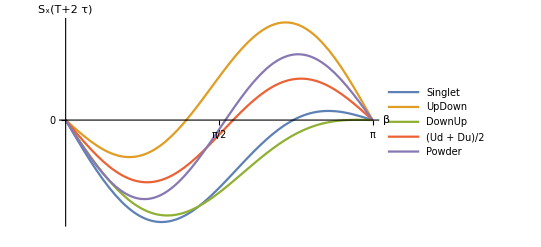

```mathematica
(*integUd = NIntegrate[Abs[xSignalUd[β, ξUd]], {β,0, π}];
integDu = NIntegrate[Abs[xSignalUd[β, -ξUd]], {β,0, π}];
integS0 = NIntegrate[Abs[xSignalS0[β, ξUd]], {β,0, π}];
integPowder = NIntegrate[Abs[xSignalPowder[β]], {β,0, π}];
integPowder2 = Plus @@ Table[Abs[xSignalPowder2[beta]], {beta, βs}];*)
nBeta = 20000;
βs = Array[#&,nBeta,{0,π}];
integUd = Plus @@ Table[Abs[xSignalUd[β, ξUd]], {β, βs}];
integDu = Plus @@ Table[Abs[xSignalUd[β, -ξUd]], {β, βs}];
integS0 = Plus @@ Table[Abs[xSignalS0[β, ξUd]], {β, βs}];
integPowder = Plus @@ Table[Abs[xSignalPowder[β]], {β, βs}];
integPowder2 = Plus @@ Table[Abs[xSignalPowder2[beta]], {beta, βs}];

plt = Plot[{xSignalS0[β, ξUd]/integS0, xSignalUd[β, ξUd]/integUd, xSignalUd[β, -ξUd]/integDu, 1/2(xSignalUd[β, ξUd]/integUd + xSignalUd[β, -ξUd]/integDu),xSignalPowder[β]/integPowder}, {β, 0, π},
AxesLabel->{β, HoldForm[Subscript[S,x][T+2τ]]},
Ticks -> {{π/2, π}, {-0.4, -0.2, 0, 0.2, 0.4, 0.6}},
PlotLegends -> LineLegend[{"Singlet","UpDown", "DownUp", "(Ud + Du)/2", "Powder"}]]
(*Export["/home/gianlum33/files/projects/oop_ciss_simulations/images/oopEseem_eckvahlParameters.jpg", plt, ImageResolution -> 400];*)
(*Export["/home/gianlum33/files/projects/oop_ciss_simulations/images/oopEseem_eckvahlParameters.pdf", plt];*)
```

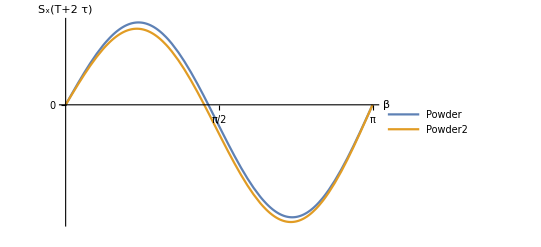

```mathematica
plt = Plot[{xSignalPowder[β]/integPowder, xSignalPowder2[β]/integPowder2}, {β, 0, π},
AxesLabel->{β, HoldForm[Subscript[S,x][T+2τ]]},
Ticks -> {{π/2, π}, {-0.4, -0.2, 0, 0.2, 0.4, 0.6}},
PlotLegends -> LineLegend[{"Powder","Powder2"}]]
```

```mathematica
test= Table[xSignalUdTau[beta, ξUd, tt], {tt, Array[#&, 10, {0, 9}]}];
(*Manipulate[Plot[test[β, ξUd, tt], {β, 0, π}], {tt, 0, 10}]*)
Plot[xSignalUdTau[beta, ξUd,  Array[#&, 10, {0, 9}]], {β, 0, π}]
```

```mathematica
√2+4
```

```mathematica
4+√2
```

```mathematica
(* From Zech Dissertation page 100*)
dd = 4.76; (* MHz nm^3*)
J = 0.03;(* MHz *)
μB = 9.27*10^(-24);
hbar = 1.05*10^(-34);
B0 = 0.35; (* T *)
g2mg1 = 0.00015; (* Valid for 
dΩ = g2mg1 μB B0/hbar * 10^(-6); (* MHz *)
τ = 2;
dmJUd = dd(1 - 3Cos[0]^2) - J;
ξUd = (dd(1 - 3Cos[0]^2) + 2J)/dΩ;
xSignalUd[β_, ξ_] := 1/2Sin[2 dmJUd τ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2);
xSignalS0[β_, ξ_] := -1/2Sin[2 dmJUd τ](1/2Sin[β]Sin[2ξ]^2+Sin[2β]Cos[ξ]^4);

nTheta = 8000;
θs = Array[#&,nTheta,{0,π}];
(*θs = Array[#&,nTheta,{0,0}];*)
t1 = Plus @@ Table[ -Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Sin[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ]]^2*
Sin[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ]]^2, {θ, θs}];
t2 = Plus @@ Table[2 Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Cos[θ]*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ]]^3 *
Sin[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ]], {θ, θs}];
t3 = Plus @@ Table[-Sin[2 (dd(1 - 3Cos[θ]^2) - J)τ]*Cos[θ]^2*
Cos[ArcTan[(dd(1 - 3Cos[θ]^2) + 2J)/dΩ]]^2, {θ, θs}];
t4 = -1/2 t1;
t5 =  -1/2 t2;
xSignalPowder[β_] := π*(Sin[β](t1 + t2) + Sin[2β](t3 + t4 + t5))

nBeta = 8000;
βs = Array[#&, nBeta, {0, π}];
(*integUd = Integrate[Abs[xSignalUd[beta, ξUd]], {beta, 0, π}];
integDu = Integrate[Abs[xSignalUd[beta, -ξUd]], {beta, 0, π}];
integS0 = Integrate[Abs[xSignalS0[beta, ξUd]], {beta, 0, π}];
integPowder = Integrate[Abs[xSignalPowder[beta]], {beta, 0, π}];*)
integUd = Plus @@ Table[Abs[xSignalUd[β, ξUd]], {β,βs}]*(π/nBeta);
integDu = Plus @@ Table[Abs[xSignalUd[β, -ξUd]], {β,βs}]*(π/nBeta);
integS0 = Plus @@ Table[Abs[xSignalS0[β, ξUd]], {β,βs}]*(π/nBeta);
integPowder = Plus @@ Table[Abs[xSignalPowder[β]], {β,βs}]*(π/nBeta);
```